```mathematica
basedir="C:\\Users\\";
files=FileNames["*.csv",basedir,1]
```

```mathematica
data=Import[#,"CSV"]&/@files;
puredata=data[[All,17;;-2]];
timems=puredata[[All,All,1]]*1000;
ydata=puredata[[All,All,2]];
datams=Transpose[{timems[[#]],ydata[[#]]}]&/@Range[Length[puredata]];
```

```mathematica
triggermod=Transpose[{timems[[6]],ydata[[6]]-10}];
```

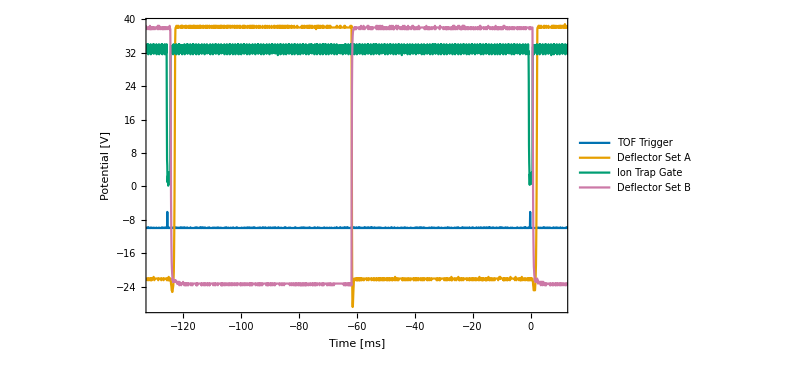

```mathematica
ListLinePlot[{triggermod,datams[[7]],datams[[9]],datams[[10]]},PlotRange->{{-130,10},All},
BaseStyle->{FontFamily->"Arial",FontSize->18},
Frame->True,FrameStyle->Directive[Black,Thick],FrameLabel->{"Time [ms]","Potential [V]"},LabelStyle->Black,
PlotStyle->{Directive[RGBColor["#0072B2"],Thick],Directive[RGBColor["#E69F00"],Thick],Directive[RGBColor["#009E73"],Thick],Directive[RGBColor["#CC79A7"],Thick]},
FrameTicks->Automatic,FrameTicksStyle->Directive[Black,Thick],
GridLines-> {None,None},GridLinesStyle->Directive[Dashed,Thick],
Axes->None,
PlotLegends->Placed[Style[#,Black,FontFamily->"Arial",18]&/@{"TOF Trigger","Deflector Set A","Ion Trap Gate","Deflector Set B"},After],
ImageSize->{600,400}]
```